## First-order system with uncertain delay (Problem 9.13)

```mathematica
Clear["Global`*"];
```

```mathematica
w=(2.1s Subscript[t, max])/(1+s Subscript[t, max]); g = 1/(1+s τ)ⅇ^(-(s Subscript[t, max])/2); t0=(g k)/(1+g k);
f = w t0 /.s->ⅈ ω; magf0 = Simplify[ComplexExpand[Abs[f]],{τ>0,Subscript[t, max]>0,k>0,ω>0}]
```

(2.1 k ω t_max)/(√((1+k^2+τ^2 ω^2+2 k Cos[(ω t_max)/2]-2 k τ ω Sin[(ω t_max)/2]) (1+ω^2 t_max^2)))

```mathematica
t0//Simplify
```

k/(k+ⅇ^((s t_max)/2) (1+s τ))

```mathematica
TeXForm[magf0]
```

\frac{2.1 k \omega  t_{\max }}{\sqrt{\left(\omega ^2 t_{\max }^2+1\right) \left(k^2-2 k \tau 
   \omega  \sin \left(\frac{\omega  t_{\max }}{2}\right)+2 k \cos \left(\frac{\omega  t_{\max
   }}{2}\right)+\tau ^2 \omega ^2+1\right)}}

```mathematica
magf=magf0/.{τ->1,Subscript[t, max]->0.1}
```

(0.21 k ω)/(√((1+0.01 ω^2) (1+k^2+ω^2+2 k Cos[0.05 ω]-2 k ω Sin[0.05 ω])))

```mathematica
dmagf=D[magf/.{τ->1,Subscript[t, max]->0.1},ω]//Simplify
```

(k (21.+21. k^2-0.21 ω^4+k (42.+1.05 ω^2+0.0105 ω^4) Cos[0.05 ω]+k ω (-19.95+0.2205 ω^2) Sin[0.05 ω]))/((100.+1. ω^2) √((1+0.01 ω^2) (1+k^2+ω^2+2 k Cos[0.05 ω]-2 k ω Sin[0.05 ω])) (1.+k^2+ω^2+2. k Cos[0.05 ω]-2. k ω Sin[0.05 ω]))

```mathematica
kwsol=FindRoot[{magf==1,dmagf==0},{{k,7},{ω,10}}]
```

{k→6.4457,ω→10.6779}

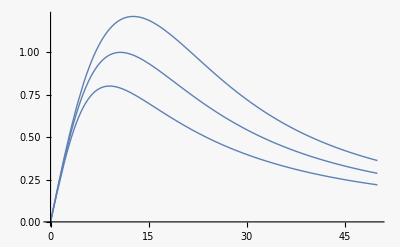

```mathematica
Plot[magf/.k->{5,6.445703948517554,8},{ω,0,50}]
```

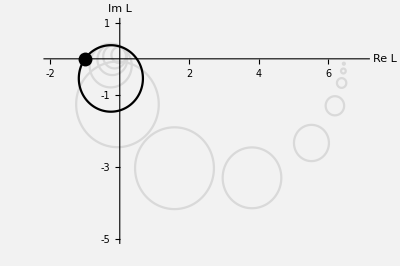

```mathematica
l=g k /.{Subscript[t, max]->0.1,τ->1,s->ⅈ ω}; r=w l/.{Subscript[t, max]->0.1,τ->1,s->ⅈ ω};
Neg1=Graphics[{PointSize[0.025],Point[{-1,0}]}];
pall=Table[ParametricPlot[{{Re[l]+Abs[r]Cos[θ],Im[l]+Abs[r]Sin[θ]}}/.{k->6.45,ω-> i},{θ,0,2π},PlotRange->{{-2,7},{-5,1}},PlotStyle->LightGray,MaxRecursion->7],{i,{0.02,0.05,0.1,0.2,0.4,0.8,1.6,5,20,30,40,60}}];
psol=ParametricPlot[{{Re[l]+Abs[r]Cos[θ],Im[l]+Abs[r]Sin[θ]}}/.{k->6.45,ω-> 10.67},{θ,0,2π},PlotRange->{{-2,7},{-5,1}},PlotStyle->{Black},MaxRecursion->7];
plotAll=Show[pall,psol,Neg1,Background->RGBColor[0.95,0.95,0.95],AxesLabel->{"Re L","Im L"},PlotLabel->None,LabelStyle->{GrayLevel[0]},BaseStyle->{FontFamily->"Gill Sans",FontSize->14},Ticks->{{-2,{1,},2,{3,},4,{5,},6,{7, }},{-5,{-4, },-3,{-2, },-1,1}}]
```

Export data.

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["firstOrderUncertainDelay1.pdf",plotAll,"PDF"]; 
*)
```

Find maximum gain for a known fixed time delay.

```mathematica
kstar=√(1+(ω τ)^2);
sol=FindRoot[Tan[(ω Subscript[t, max])/2]+ω τ==0/.{Subscript[t, max]->0.1,τ->1},{ω,32}][[1]]
```

ω→32.0399

```mathematica
kmax=N[kstar/.{τ->1,sol}]
```

32.0555

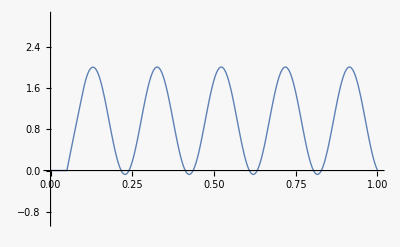

```mathematica
sys=TransferFunctionModel[t0,s]//Simplify;
ysol=OutputResponse[sys/.{Subscript[t, max]->0.1,τ->1,k->kmax},UnitStep[t],{t,0,1}];
Plot[ysol,{t,0,1},PlotRange->{-1,3}]
```

Repeat for maximum possible time delay

```mathematica
sol2=FindRoot[Tan[(ω Subscript[t, max])/2]+ω τ==0/.{Subscript[t, max]->0.2,τ->1},{ω,16}][[1]]
```

ω→16.3199

```mathematica
kmax=N[kstar/.{τ->1,sol2}]
```

16.3506

Plot T (closed-loop transfer function) and W^-1

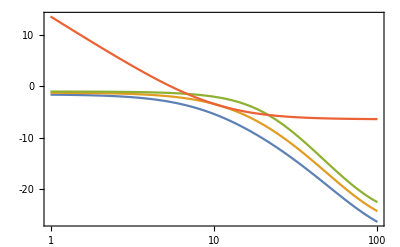

```mathematica
winvtf=TransferFunctionModel[1/w/. Subscript[t, max]->0.1,s];
T0=(g k)/(1+g k) /.{Subscript[t, max]->0.1,τ->1};
Ttf=TransferFunctionModel[T0/.k->{5,6.45,8},s];
BodePlot[{Ttf,winvtf},{1,100},PlotLayout->"Magnitude"]
```

```mathematica
(g k)/(1+g k)//Simplify
```

k/(k+ⅇ^((s t_max)/2) (1+s τ))

```mathematica
w
```

(2.1 s t_max)/(1+s t_max)